## PT-sym

```mathematica
Clear[ham,en,fn1,fn2];

ham[kx_,ky_]=({{-ϵ, kx+ϵ, ϵ(1+ⅈ)}, {kx-ϵ, 0, (ky-ϵ)(1+ⅈ)}, {-ϵ(1-ⅈ), (ky+ϵ)(1-ⅈ), ϵ}});lim=0.01;
det[kx_,ky_,ϵ_]=-Det[(ham[kx_,ky_,ϵ_]=({{-ϵ, kx+ϵ, ϵ(ⅈ+1)}, {kx-ϵ, 0, (ky-ϵ)(1+ⅈ)}, {ϵ(ⅈ-1), (ky+ϵ)(1-ⅈ), ϵ}}))-en IdentityMatrix[3]];
dat1=Flatten[Table[{kx,ky,Sort[Abs[Eigenvalues[ham[kx,ky,0.1]]]][[1]]},{kx,-0.15,0.15,0.005},{ky,-0.5,0.5,0.05}],1];
dat2=Flatten[Table[{kx,ky,Sort[Abs[Eigenvalues[ham[kx,ky,0.1]]]][[2]]},{kx,-0.15,0.15,0.005},{ky,-0.5,0.5,0.05}],1];
dat3=Flatten[Table[{kx,ky,Sort[Abs[Eigenvalues[ham[kx,ky,0.1]]]][[3]]},{kx,-0.15,0.15,0.005},{ky,-0.5,0.5,0.05}],1];
ListPlot3D[{dat1,dat2,dat3},PlotRange->All,AxesLabel->{"k_x","k_y","Abs[E]"},ImageSize->Medium]
SeriesCoefficient[det[kx,ky,ϵ],{en,0,3}]
A[kx_,ky_,ϵ_]=SeriesCoefficient[det[kx,ky,ϵ],{en,0,2}];
B[kx_,ky_,ϵ_]=SeriesCoefficient[det[kx,ky,ϵ],{en,0,1}];
CC[kx_,ky_,ϵ_]=SeriesCoefficient[det[kx,ky,ϵ],{en,0,0}];
p[kx_,ky_,ϵ_]=B[kx,ky,ϵ]/3−(A[kx,ky,ϵ])^2/9;
q[kx_,ky_,ϵ_]=−CC[kx,ky,ϵ]/2+(A[kx,ky,ϵ] B[kx,ky,ϵ])/6−(A[kx,ky,ϵ])^3/27;
```

-Graphics3D-

1

```mathematica
p[kx,ky,ϵ]
q[kx,ky,ϵ]//FullSimplify
```

1/3 (-kx^2-2 ky^2+4 ϵ^2)

-1/2 ϵ (kx^2-2 ky^2-4 kx ϵ+4 ky ϵ+ϵ^2)

```mathematica
Clear[eq1,eq2,nsol];(* q+√(q^2+p^3) *)
eq1=(p[kx,ky,0.1]//TrigToExp)/.{kx->-ⅈ Log[ux],ky->-ⅈ Log[uy]}//FullSimplify;
eq2=(q[kx,ky,0.1]//TrigToExp)/.{kx->-ⅈ Log[ux],ky->-ⅈ Log[uy]}//FullSimplify;
nsol=NSolve[{eq1==0 && eq2==0},{ux,uy}];
For[i=1,i≤Length[nsol],i++,Print[i," kx= ",Chop[-ⅈ Log[ux]/.nsol[[i]]],"; ky= ",Chop[-ⅈ Log[uy]/.nsol[[i]]]]]
Length[nsol]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

1 kx= 0.21228+0.0807042 ⅈ; ky= 0.0945314-0.090615 ⅈ

2 kx= -0.118579; ky= -0.113884

3 kx= 0.0940181; ky= 0.124821

4 kx= 0.21228-0.0807042 ⅈ; ky= 0.0945314+0.090615 ⅈ

4

```mathematica
exp=Eigenvalues[(ham[-ⅈ Log[ux]+0  ,-ⅈ Log[uy]+ ky,0.1]/.nsol[[2]])]//Chop;Print["For ",2," eigenvalues ","\n", "en1=",Normal[FullSimplify[Chop[Series[exp[[1]],{ky,0,1}]]]](**),"\n","en2=", Normal[FullSimplify[Chop[Series[exp[[2]],{ky,0,1}]]]],"\n", "en3=",Normal[FullSimplify[Chop[Series[exp[[3]],{ky,0,1}]]]]]
```

Root::sbr: Because of branch cuts, the series may represent a different root of -0.0427768 ky+0.1 ky^2+(-0.227768 ky+1. ky^2) #1-0.5 #1^3& for some values of ky.

General::stop: Further output of Root::sbr will be suppressed during this calculation.

For 2 eigenvalues 
en1=-0.440635 ky^(1/3)+0.344605 ky^(2/3)
en2=(0.220318-0.381601 ⅈ) ky^(1/3)-(0.172302+0.298437 ⅈ) ky^(2/3)
en3=(0.220318+0.381601 ⅈ) ky^(1/3)-(0.172302-0.298437 ⅈ) ky^(2/3)

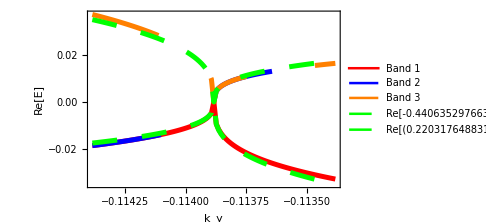

```mathematica
kx0=-0.1185789490043181;ky0=-0.11388378473916148;
Clear[dat1];
(*kx0=0.0940180571818742;ky0= 0.12482108180060336;*)
lim=0.00001;l0=0.0005;
dat0=Table[{ky+ky0,Re[-0.4406352976638015 ky^(1/3)]},{ky,-l0,l0,lim}];
dat00=Table[{ky+ky0,Re[(0.22031764883190075-0.38160136158097 ⅈ) ky^(1/3)]},{ky,-l0,l0,lim}];
dat1=Table[{kep+ky0,Sort[Re[Eigenvalues[ham[kx0,ky0+kep ,0.1]]]][[1]]},{kep,-l0,l0,lim}];
dat2=Table[{kep+ky0,Sort[Re[Eigenvalues[ham[kx0,ky0+kep,0.1]]]][[2]]},{kep,-l0,l0,lim}];
dat3=Table[{kep+ky0,Sort[Re[Eigenvalues[ham[kx0,ky0+kep ,0.1]]]][[3]]},{kep,-l0,l0,lim}];
pl=ListLinePlot[{dat1,dat2,dat3,dat0,dat00},PlotRange->All,ImageSize->Medium,PlotStyle->{Directive[Red,Thickness[0.01]],Directive[Dashing[0.2],Blue,Thickness[0.01]],Directive[Dashing[0.2],Orange,Thickness[0.01]],Directive[Dashing[0.05],Green,Thickness[0.01]],Directive[Dashing[0.05],Green,Thickness[0.01]]},Frame->True,FrameLabel->{"k_y","Re[E]"},RotateLabel->False,LabelStyle->Directive[Medium],Axes->False,PlotLegends->{"Band 1","Band 2","Band 3","Re[-0.4406352976638015` (ky-ky0)^(1/3)]","Re[(0.22031764883190075`-0.38160136158097` ⅈ) (ky-ky0)^(1/3)]"}]
SetDirectory[NotebookDirectory[]];
Export["1d.jpg",pl,ImageResolution->500];
```

```mathematica
dat=Table[{ky0+ky,Sort[Re[Eigenvalues[ham[kx0,ky0+ky,0.1]]]][[3]]},{ky,0,0.5,0.00001}];
fit=FindFit[%, a ky^(1/3),{a},ky]
```

{a→0.403348-0.0143915 ⅈ}

## P-sym

```mathematica
Eigenvalues[hp]
```

{0,-ⅈ √(-kx^2-ky^2-kx ϵ+(1-ⅈ) ky ϵ),ⅈ √(-kx^2-ky^2-kx ϵ+(1-ⅈ) ky ϵ)}

```mathematica
Clear[hamp,en,fn1,fn2];

hamp[kx_,ky_]=({{0, (ⅈ kx)+(ⅈ )/10, 0}, {(-ⅈ kx), 0, (ⅈ ky)}, {0, (-ⅈ ky)+(1+ⅈ )/10, 0}});lim=0.01;
en[kx_,ky_]=FullSimplify[Eigenvalues[hamp[kx,ky]],Assumptions->{kx,ky}∈ Reals]
FullSimplify[Eigenvectors[hamp[kx,ky]],Assumptions->{kx,ky}∈ Reals]//FullSimplify;
fn1=FullSimplify[Re[(en[kx,ky][[2]])^2],Assumptions->{kx,ky}∈Reals]
fn2=FullSimplify[Im[(en[kx,ky][[2]])^2],Assumptions->{kx,ky}∈Reals]
Solve[fn1==0 && fn2==0,{kx,ky}]
dat2=Flatten[Table[{kx,ky,Sort[Abs[Eigenvalues[hamp[kx,ky]]]][[2]]},{kx,-0.2,0.2,lim},{ky,-0.2,0.2,lim}],1];
dat3=Flatten[Table[{kx,ky,-Sort[Abs[Eigenvalues[hamp[kx,ky]]]][[3]]},{kx,-0.2,0.2,lim},{ky,-0.2,0.2,lim}],1];
ListPlot3D[{dat2,dat3},PlotRange->All,AxesLabel->{"k_x","k_y","Abs[E]"},ImageSize->Medium]
```

{0,-(√(kx+10 kx^2-(1-ⅈ) ky+10 ky^2))/(√10),(√(kx+10 kx^2-(1-ⅈ) ky+10 ky^2))/(√10)}

kx/10+kx^2-ky/10+ky^2

ky/10

{{kx→0,ky→0},{kx→-1/10,ky→0}}

```mathematica
ComplexExpand[ReIm[kx+10 kx^2-(1-ⅈ) ky+10 ky^2]]
Solve[ky==0 && kx+10 kx^2-ky+10 ky^2==0,{kx,ky}]
```

{kx+10 kx^2-ky+10 ky^2,ky}

{{kx→0,ky→0},{kx→-1/10,ky→0}}

```mathematica
Clear[exp];exp=FullSimplify[Eigenvalues[(hamp[kx,ky]/.{kx->0 ,ky->0+ky})],Assumptions->{kx,ky}∈ Reals];
FullSimplify[Series[exp[[2]],{ky,0,2}],Assumptions->{kx,ky}∈ Reals && ky>0]//Normal//N
FullSimplify[Series[exp[[3]],{ky,0,3}],Assumptions->{kx,ky}∈ Reals && ky>0]//Normal//N
```

(-0.143912-0.347434 ⅈ) √ky-(0.508806-1.22837 ⅈ) ky^(3/2)

(0.143912+0.347434 ⅈ) √ky+(0.508806-1.22837 ⅈ) ky^(3/2)+(2.17147-0.89945 ⅈ) ky^(5/2)

```mathematica
Abs[√(-1/10.0+ⅈ/10) √-1]
Abs[√(-1/10.0+ⅈ/10) ]
```

0.37606

0.37606

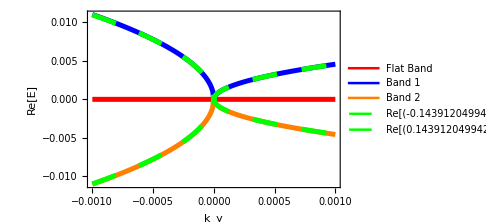

```mathematica
lim=0.00001;bd=lim*100;
fn[kx_,ky_]=(√(kx+10 kx^2-(1-ⅈ) ky+10 ky^2))/(√10);
dat0=Table[{ky,Re[(-0.14391204994250748-0.3474344227601157 ⅈ) √ky]},{ky,-bd,bd,lim}];
dat00=Table[{ky,Re[(0.14391204994250748+0.3474344227601157 ⅈ) √ky]},{ky,-bd,bd,lim}];
dat11=Table[{ky,-0.752 √ky},{ky,-bd,bd,lim}];
dat1x=Table[{ky,0},{ky,-bd,bd,lim}];
dat2x=Table[{ky,Re[fn[0,ky]]},{ky,-bd,bd,lim}];
dat3x=Table[{ky,-Re[fn[0,ky]]},{ky,-bd,bd,lim}];
pl2=ListLinePlot[{dat1x,dat2x,dat3x,dat0,dat00},PlotRange->All,ImageSize->Medium,PlotStyle->{Directive[Red,Thickness[0.01]],Directive[(*Dashing[0.1],*)Blue,Thickness[0.01]],Directive[(*Dashing[0.1],*)Orange,Thickness[0.01]],Directive[Dashing[0.05],Green,Thickness[0.01]],Directive[Dashing[0.05],Green,Thickness[0.01]]},Frame->True,FrameLabel->{"k_y","Re[E]"},RotateLabel->False,LabelStyle->Directive[Medium],Axes->False,PlotLegends->{"Flat Band","Band 1","Band 2","Re[(-0.14391204994250748`-0.3474344227601157` ⅈ) √ky]","Re[(0.14391204994250748`+0.3474344227601157` ⅈ) √ky]"}]
SetDirectory[NotebookDirectory[]];
Export["1e.jpg",pl2,ImageResolution->500];
```

```mathematica
dat=Table[{ky,Abs[fn[-0.1,ky]]},{ky,0,0.00005,0.0000001}];
FindFit[%,a √ky,{a},ky]
dat=Table[{ky,Abs[fn[-0.1,ky]]},{ky,-0.00005,0,0.0000001}];
FindFit[%,a Abs[√ky],{a},ky]
```

{a→0.752058}

{a→0.752183}